Seth AbuHamdeh

ID:34937889

Problem 1

```mathematica
f[x_] := x^3-4*(x^2)+x+4
```

```mathematica
f[2]
```

-2

Problem 2

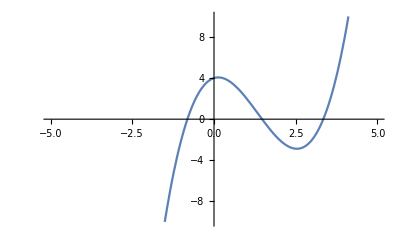

```mathematica
Plot[f[x], {x,-5,5} ,PlotRange-> {-10,10}]
```

Problem 3

```mathematica
newt3Steps[z_] := NestList[N[#-f[#]/f'[#]&], z,3]
```

Problem 4

```mathematica
newt3Steps[2]
```

{2,1.33333,1.47009,1.47068}

Problem 5

```mathematica
myRules = NSolve[f[x]]
rootList = x /.myRules
```

{{x→-0.813607},{x→1.47068},{x→3.34292}}

{-0.813607,1.47068,3.34292}

Problem 6

```mathematica
Abs[1.5-rootList]
```

{2.31361,0.0293166,1.84292}

Problem 7

```mathematica
newtWhile[z_] := N[NestWhileList[#-f[#]/f'[#]&,z,Abs[f[#]]> .01&]]
```

Problem 8

```mathematica
newtWhile[2.8]
```

{2.8,4.03019,3.5429,3.36785,3.34339}

Problem 10

```mathematica
newList = Table[newtWhile[i],{i,2,4,.01}];
```

Problem 11: 8 starting values.

```mathematica
lengthmyList = Table[Length[i],{i,newList}];
Count[lengthmyList, x_/; x >= 10]
```

8

Problem 12

```mathematica
Max[lengthmyList]
```

14

```mathematica
Position[lengthmyList, x_/; x == 14]
```

{{54},{55}}

Problem 13

```mathematica
z1 = 2.54;
z2 = 2.53;
newt1 = newtWhile[z1]
newt2 = newtWhile[z2]
```

{2.54,85.2795,57.3089,38.6675,26.2485,17.9819,12.4898,8.85668,6.47667,4.95236,4.02813,3.54198,3.36764,3.34338}

{2.53,-74.6636,-49.344,-32.4707,-21.2314,-13.753,-8.78932,-5.51355,-3.38072,-2.03735,-1.26101,-0.906197,-0.818909,-0.813625}